## Lecture 1

```mathematica
BivariateNormalPDF[{x_,y_},μ_,Σ_]:=Module[{ΣDet,ΣInv,d,normConst,exponent},(*Compute determinant and inverse of covariance matrix*)
ΣDet=Det[Σ];
ΣInv=Inverse[Σ];
(*Dimensionality (should be 2)*)
d=Length[μ];
(*Normalization constant*)
normConst=1/((2 π)^(d/2) Sqrt[ΣDet]);
(*Exponent term with proper vector subtraction*)
exponent=-1/2 (({x,y}-μ).ΣInv.({x,y}-μ));
(*Return the density function*)
normConst Exp[exponent]];
```

```mathematica
μ={0,0}; (*Mean vector*)
Σ={{1,0.5},{0.5,1}}; (*Covariance matrix*)
BivariateNormalPDF[{1,1},μ,Σ]
```

0.0943539

## Lecture 2

```mathematica
Gamma[x]/Gamma[x-1] //FullSimplify
```

-1+x

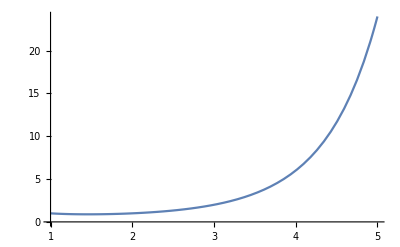

```mathematica
Plot[Gamma[x],{x,1,5}]
```

```mathematica
ComplexPlot3D[Gamma[z],{z,-1-1I,1+1I},PlotLegends ->Automatic]
```

```mathematica
Integrate[x^a*(1-x)^(b-1),{x,0,1},Assumptions->{a>0,b>0}]
```

(Gamma[1+a] Gamma[b])/Gamma[1+a+b]